```mathematica
LagrangePolyFactor[j_,k_,xp_]:=If[j!=k,((x-xp[[k]])/(xp[[j]]-xp[[k]])),1]
LagrangePoly[j_,xp_]:=Product[If[j!=k,((x-xp[[k]])/(xp[[j]]-xp[[k]])),1],{k,1,Length[xp]}]
```

### Equal Spacing

{-1,-1/3,1/3,1}

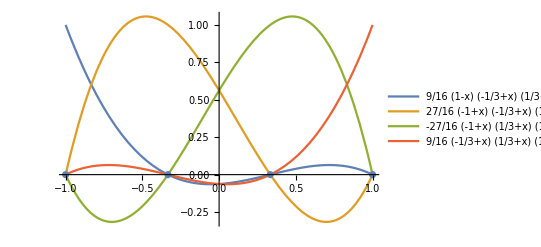

{-0.0083125,0.0511875,0.9725625,-0.0154375}

{0.248125,-1.569375,0.894375,0.426875}

```mathematica
order=3;
xp=Subdivide[-1,1,order]
Points=Table[{xp[[n]],0},{n,1,order+1}];
Bases=Table[LagrangePoly[n,xp],{n,1,order+1}];
Show[Plot[Bases,{x,-1,1},PlotRange->Full,PlotLegends->"Expressions"],ListPlot[Points]]
NumberForm[Bases/.x->0.3,14]
NumberForm[D[Bases,x]/.x->0.3,14]
```

### Gauss-Lobatto Spacing

{-1.,-0.447214,0.447214,1.}

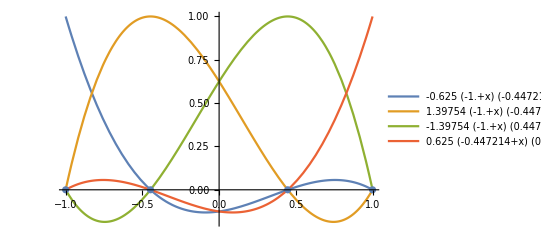

{-0.048125,0.1872209013391,0.9502790986609,-0.089375000000001}

{0.33125,-1.3952060147343,0.64520601473428,0.41875}

```mathematica
GaussLobattoPointsWeights=ResourceFunction["ModifiedGaussianQuadratureWeights"]["Lobatto",order+1];
xp=Table[GaussLobattoPointsWeights[[n,1]],{n,1,order+1}]
Points=Table[{xp[[n]],0},{n,1,order+1}];
Bases=Table[LagrangePoly[n,xp],{n,1,order+1}];
Show[Plot[Bases,{x,-1,1},PlotRange->Full,PlotLegends->"Expressions"],ListPlot[Points]]
NumberForm[Bases/.x->0.3,14]
NumberForm[D[Bases,x]/.x->0.3,14]
```

```mathematica
NumberForm[MatrixForm[GaussLobattoPointsWeights=ResourceFunction["ModifiedGaussianQuadratureWeights"]["Lobatto",9]],14]
```

(-1. | 0.027777777777777
-0.89975799541146 | 0.16549536156081
-0.67718627951074 | 0.27453871250016
-0.36311746382618 | 0.34642851097305
-4.4408920985006×10^-16 | 0.37151927437642
0.36311746382618 | 0.34642851097305
0.67718627951074 | 0.27453871250016
0.89975799541146 | 0.16549536156081
1. | 0.027777777777778)

```mathematica
1/.066666666666665
```

15.

```mathematica
1/"0.37847495629785"
```

2.64218

```mathematica
1/0.55485837703549
```

1.80226

## 3 D product

```mathematica
GLp1=ResourceFunction["ModifiedGaussianQuadratureWeights"]["Lobatto",order+2];
NumberForm[evalPoints=Chop[Table[GLp1[[n,1]],{n,1,order+2}],10^-14],14]
```

{-1.,-0.65465367070798,0,0.65465367070798,1.}

```mathematica
TPBasis3[a_,b_,c_,ξ0_,ξ1_,ξ2_]:=(Bases[[a]]/.x->ξ0)(Bases[[b]]/.x->ξ1)(Bases[[c]]/.x->ξ2)
DTPBasis3[a_,b_,c_,ξ0_,ξ1_,ξ2_]:={ D[TPBasis3[a,b,c,x,ξ1,ξ2],x]/.x->ξ0,
									D[TPBasis3[a,b,c,ξ0,x,ξ2],x]/.x->ξ1,
									D[TPBasis3[a,b,c,ξ0,ξ1,x],x]/.x->ξ2}
```

```mathematica
TPBasis3[2,1,1,ξ0,ξ1,ξ2]
D[TPBasis3[2,1,1,ξ0,ξ1,ξ2],ξ0]
```

0.545915 (-1.+ξ0) (-0.447214+ξ0) (1.+ξ0) (-1.+ξ1) (-0.447214+ξ1) (0.447214+ξ1) (-1.+ξ2) (-0.447214+ξ2) (0.447214+ξ2)

0.545915 (-1.+ξ0) (-0.447214+ξ0) (-1.+ξ1) (-0.447214+ξ1) (0.447214+ξ1) (-1.+ξ2) (-0.447214+ξ2) (0.447214+ξ2)+0.545915 (-1.+ξ0) (1.+ξ0) (-1.+ξ1) (-0.447214+ξ1) (0.447214+ξ1) (-1.+ξ2) (-0.447214+ξ2) (0.447214+ξ2)+0.545915 (-0.447214+ξ0) (1.+ξ0) (-1.+ξ1) (-0.447214+ξ1) (0.447214+ξ1) (-1.+ξ2) (-0.447214+ξ2) (0.447214+ξ2)

```mathematica
Baselines=Table[TPBasis3[a,b,c,evalPoints[[i]],evalPoints[[j]],evalPoints[[k]]],
{i,1,order+2},{j,1,order+2},{k,1,order+2},
{a,1,order+1},{b,1,order+1},{c,1,order+1}];
Dimensions[Baselines]
NumberForm[Chop[Baselines,10^-14],14]
```

{5,5,5,4,4,4}

{1}
 |  |  |  |

```mathematica
Bases
```

{-0.625 (-1.+x) (-0.447214+x) (0.447214+x),1.39754 (-1.+x) (-0.447214+x) (1.+x),-1.39754 (-1.+x) (0.447214+x) (1.+x),0.625 (-0.447214+x) (0.447214+x) (1.+x)}

```mathematica
GradientBaselines=Table[DTPBasis3[a,b,c,evalPoints[[i]],evalPoints[[j]],evalPoints[[k]]],
{i,1,order+2},{j,1,order+2},{k,1,order+2},
{a,1,order+1},{b,1,order+1},{c,1,order+1}];
Dimensions[GradientBaselines]
NumberForm[Chop[GradientBaselines,10^-14],14]
```

{5,5,5,4,4,4,3}

{{{1},3,{1}},3,{{1},{1},{{1},{1},{1},{1,{1},{1},{1}},{1}},{1},{1}}}
 |  |  |  |